```mathematica
Infty:=4
phi[u_]:=NSum[(2*Pi^2*n^4*Exp[9*u]-3*Pi*n^2*Exp[5*u])*Exp[-Pi*n^2*Exp[4*u]], {n, 1, Infty}]
dH[n_, z_, u_]:=Function[t, Evaluate[D[phi[t], {t, n}]]][u]*Cos[z*u]
H[n_, z_]:=NIntegrate[dH[n, z, u], {u, 0, Infty}]
```

```mathematica
dH[n_, u_]:=Function[t, Evaluate[D[phi[t], {t, n}]]][u]
Quiet[Table[Boole[Abs[dH[n+1, 0]]>Abs[dH[n, 0]]], {n, 0, 20}]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
phi[u_]:=NSum[(2*Pi^2*n^4*Exp[9*u]-3*Pi*n^2*Exp[5*u])*Exp[-Pi*n^2*Exp[4*u]], {n, 1, 4}]
R1:=Sum[k^4*Exp[-Pi*k^2], {k, 1, Infinity}]
R1:=Sum[k^2*Exp[-Pi*k^2], {k, 1, Infinity}]
dphi[n_]:=2*Pi^2*(9-4*Pi*n^2)^n*R1-3*Pi*(5-4*Pi*n^2)^n*R2
DiscretePlot[Function[t, Evaluate[D[phi[t], {t, n}]]][0], {n, 0, 3}]
```

NSum::nsnum: Summand (or its derivative) (2 π^2 n^4 Exp[9 t]-3 π n^2 Exp[5 t]) Exp[-π n^2 Exp[4 t]] is not numerical at point n = 1.

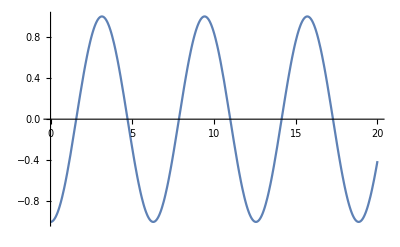

```mathematica
FractionalD[α_,f_,x_,opts___]:=Integrate[(x-t)^(-α-1) (f/.x->t),{t,0,x},opts,GenerateConditions->False]/Gamma[-α]
FractionalD[α_?Positive,f_,x_,opts___]:=Module[{m=Ceiling[α]},If[α∈Integers,D[f,{x,α}],D[FractionalD[-(m-α),f,x,opts],{x,m}]]]

f[x_]:=Sin[x]
Plot[Evaluate[FractionalD[3,f[x],x]], {x, 0, 20}]
```